## Higgs decays in the Standard Model

## Initialization cells

#### Setup

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts = True;
<<FeynCalc`;
$FAVerbose=0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Global`$FeynCalcStartupMessages::shdw: Symbol $FeynCalcStartupMessages appears in multiple contexts {Global`,FeynCalc`}; definitions in context Global` may shadow or be shadowed by other definitions.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, in preparation

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

#### Settings

```mathematica
$BreitMaison=True;
$Larin=False;
(*$West=False;*)
$Assumptions={MH>0,MQD[Index[Generation,4]]>0,MQU[Index[Generation,4]]>0,MLE[Index[Generation,4]]>0,SMP["m_H"]>0,SMP["m_W"]>0,SMP["m_b"]>0, SMP["m_t"]> 0,SMP["m_tau"]>0,SMP["m_W"]>0};
```

#### Definitions

```mathematica
LandauGauge={GaugeXi->0};
FeynmanGauge={GaugeXi-> 1};
YennieGauge={GaugeXi->3};
preFactor=-ⅈ/(2 π)^D; (*Prefactor that comes with the momentum integration*)
replaceFac1={MQD[_,_]:> SMP["m_b"],MQU[_,_]:> SMP["m_t"],MLE[_]:> SMP["m_e"],yd[_,_]:> Sqrt[2]SMP["e"]SMP["m_b"]/(2SMP["m_W"]SMP["sin_W"]),yu[_,_]:> Sqrt[2]SMP["e"]SMP["m_t"]/(2SMP["m_W"]SMP["sin_W"]),yl[_,_]:>Sqrt[2] SMP["e"]SMP["m_e"]/(2SMP["m_W"]SMP["sin_W"]),MW:> SMP["m_W"],MZ:> SMP["m_Z"],EL:> SMP["e"],sw:> SMP["sin_W"],cw:> SMP["cos_W"],g1z:> SMP["g_Z"],sz:> SMP["sin_Z"],cz:> SMP["cos_Z"],sg->  SMP["sin_G"],cg->  SMP["cos_G"],sa->  SMP["sin_H"],ca->  SMP["cos_H"],lam1-> (SMP["cos_H"]^2SMP["m_H"]^2+SMP["sin_H"]^2MH2^2)/2/vev^2,lam3->SMP["cos_H"]SMP["sin_H"] (MH2^2-SMP["m_H"]^2)/(Sqrt[RR*vev^2]vev)};
replaceFac2={vev-> 2SMP["m_W"]SMP["sin_W"]/SMP["e"]};
smLimit={SMP["sin_Z"]:> 0,SMP["cos_Z"]:> 1,SMP["sin_G"]:> 0,SMP["cos_G"]:> 1,SMP["g_Z"]:> 0,SMP["sin_H"]:> 0,SMP["cos_H"]:> 1};
```

```mathematica
(*The replacements above are just for presentation. The file SMP.m (attached) can be put in the ~/../Applications/FeynCalc/Feynma folder. You can also add your own graphics in the SMP.m file*)
```

#### Setup

```mathematica
If[ $FrontEnd === Null,
		$FeynCalcStartupMessages = False;
		Print["Computation of the 1-loop gluon self-energy in QCD"];
];
$LoadAddOns={"FeynHelpers"};
$LoadFeynArts = True;
<<FeynCalc`;
$FAVerbose=0;
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

#### Settings

```mathematica
$BreitMaison=True;
$Larin=False;
(*$West=False;*)
$Assumptions={MH>0,MQD[Index[Generation,4]]>0,MQU[Index[Generation,4]]>0,MLE[Index[Generation,4]]>0,SMP["m_H"]>0,SMP["m_W"]>0,SMP["m_b"]>0, SMP["m_t"]> 0,SMP["m_tau"]>0,SMP["m_W"]>0};
```

#### Definitions

```mathematica
LandauGauge={GaugeXi->0};
FeynmanGauge={GaugeXi-> 1};
YennieGauge={GaugeXi->3};
preFactor=-ⅈ/(2 π)^D;
replaceFac1={MQD[_,_]:> SMP["m_b"],MQU[_,_]:> SMP["m_t"],MLE[_]:> SMP["m_e"],yd[_,_]:> Sqrt[2]SMP["e"]SMP["m_b"]/(2SMP["m_W"]SMP["sin_W"]),yu[_,_]:> Sqrt[2]SMP["e"]SMP["m_t"]/(2SMP["m_W"]SMP["sin_W"]),yl[_,_]:>Sqrt[2] SMP["e"]SMP["m_e"]/(2SMP["m_W"]SMP["sin_W"]),MW:> SMP["m_W"],MZ:> SMP["m_Z"],EL:> SMP["e"],sw:> SMP["sin_W"],cw:> SMP["cos_W"],g1z:> SMP["g_Z"],sz:> SMP["sin_Z"],cz:> SMP["cos_Z"],sg->  SMP["sin_G"],cg->  SMP["cos_G"],sa->  SMP["sin_H"],ca->  SMP["cos_H"],lam1-> (SMP["cos_H"]^2SMP["m_H"]^2+SMP["sin_H"]^2MH2^2)/2/vev^2,lam3->SMP["cos_H"]SMP["sin_H"] (MH2^2-SMP["m_H"]^2)/(Sqrt[RR*vev^2]vev),ZH-> SMP["z_H"]};
replaceFac2={Zu-> Zq+SMP["z_H"],Zd-> Zq-SMP["z_H"],Ze-> Zl-SMP["z_H"],vev-> 2SMP["m_W"]SMP["sin_W"]/SMP["e"],SMP["cos_G"]:> SMP["m_W"](SMP["cos_Z"]SMP["e"]-SMP["z_H"]SMP["g_Z"]SMP["sin_Z"]SMP["sin_W"]SMP["cos_W"])/(SMP["cos_W"]SMP["e"]SMP["m_Z"]),SMP["sin_G"]:> SMP["m_W"](SMP["sin_Z"]SMP["e"]+SMP["z_H"]SMP["g_Z"]SMP["cos_Z"]SMP["sin_W"]SMP["cos_W"])/(SMP["cos_W"]SMP["e"]SMP["m_Zp"]),(SMP["cos_W"])^2-> 1-(SMP["sin_W"])^2};

replaceFacNoMix={SMP["cos_Z"]:> 1,SMP["sin_Z"]:> 0,SMP["cos_G"]:> 1,SMP["sin_G"]:> 0,SMP["z_H"]:> 0 };smLimit={SMP["sin_Z"]:> 0,SMP["cos_Z"]:> 1,SMP["sin_G"]:> 0,SMP["cos_G"]:> 1,SMP["g_Z"]:> 0,SMP["sin_H"]:> 0,SMP["cos_H"]:> 1};
replaceFacAnomaly={Ey:> -3/2(Zl+3Zq),K2:> -3(Zl+3Zq),Ez:> -3/4 SMP["z_H"](Zl+3Zq),Cz:> -9/(4MI) SMP["z_H"](Zl+3Zq),D2:>3/(MI)(Zl+3Zq),Cy:> -3/(2MI)(Zl+3Zq),Cx:> -3a/(2MI)(-SMP["z_H"]^3-3 SMP["z_H"] Zl^2-Zl^3+3SMP["z_H"]^2(Zl+6Zq))}; 
replaceFacMassless={SMP["m_b"]:> 0,SMP["m_t"]:> 0,SMP["m_e"]:> 0};
```

```mathematica
replaceFacAmp={Log[(2SMP["m_b"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_b"]^2SMP["m_Z"]^2])/(2SMP["m_b"]^2)]:> AbZ,Log[(2SMP["m_b"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_b"]^2SMP["m_Zp"]^2])/(2SMP["m_b"]^2)]:> AbZp,Log[(2SMP["m_t"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_t"]^2SMP["m_Z"]^2])/(2SMP["m_t"]^2)]:> AtZ,Log[(2SMP["m_t"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_t"]^2SMP["m_Zp"]^2])/(2SMP["m_t"]^2)]:> AtZp,Log[(2SMP["m_e"]^2-SMP["m_Z"]^2+Sqrt[SMP["m_Z"]^4-4SMP["m_e"]^2SMP["m_Z"]^2])/(2SMP["m_e"]^2)]:> AeZ,Log[(2SMP["m_e"]^2-SMP["m_Zp"]^2+Sqrt[SMP["m_Zp"]^4-4SMP["m_e"]^2SMP["m_Zp"]^2])/(2SMP["m_e"]^2)]:> AeZp};
```

```mathematica
log[x_ y_]:= log[x]+log[y]
log[x_ /y_]:= log[x]-log[y]
log[x_ ^y_]:=y log[x]
```

# QCD examples

## q1 q2>q1 q2

### The calculation

#### Creating amplitudes

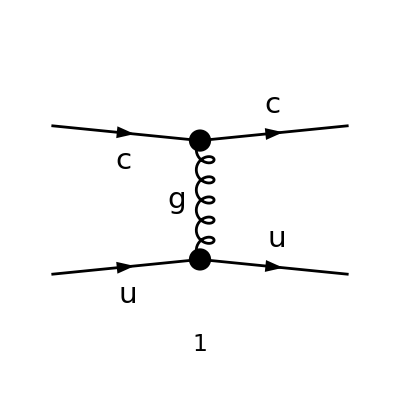

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{2}],F[3,{1}]}->{F[3,{2}],F[3,{1}]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
Clear[amp]
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&
```

-(g_s^2 T_Col3Col1^Glu5 T_Col4Col2^Glu5 (φ(OverBar[k1],m_c)).(γ̄)^Lor2.(φ(OverBar[p1],m_c)) (φ(OverBar[k2],m_u)).(γ̄)^Lor2.(φ(OverBar[p2],m_u)))/(OverBar[k2]-OverBar[p2])^2

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[amp[0]*ComplexConjugate[amp[0]]]]]]//SUNSimplify[#,Explicit->True]&
```

(C_A C_F g_s^4 (2 m_c^2 (-2 m_μ^2+4 m_u^2+t)-2 m_e^2 (-2 m_μ^2+2 m_u^2+s+u)+2 m_e^4+2 m_μ^4-2 s m_μ^2+2 t m_u^2-2 u m_μ^2+s^2+u^2))/t^2

```mathematica
ampSquaredMassless1[0]=Simplify[(#1/. {SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0}&)[ampSquared[0]]]//Simplify
```

(C_A C_F g_s^4 (s^2+u^2))/t^2

# Group algebra and integrals

```mathematica
CAN=3;
CFN=8/(2*3);
dAN=8;
dFN=3;
TFN=1/2;
TAN=3;
RepComp={CA->CAN,CF->CFN,dA->dAN,dF->dFN,TA->TAN,TF->TFN};
```

```mathematica
RepCompW={CAW->2,CFW->(2^2-1)/(2*2),dAW->2^2-1,dFW->2,TAW->2,TFW->1/2};
```

```mathematica
mDW=1/6(2*3+5)*2 gw^2/.RepCompW;
mFW=1/8 CFW*2 gw^2/.RepCompW;
```

```mathematica
mD=1/6(CA+3*CF*dF/dA)*2 g^2/.RepComp;
mF=1/8 CF*2 g^2/.RepComp;
```

```mathematica
gwN=Sqrt[1/30*4 π]//N;
```

```mathematica
gSN=Sqrt[0.12*4 π]//N;
```

```mathematica
mD/.g->gSN
```

2.26195

```mathematica
meffg=1/2 mD;
meffF=2 mF;
```

## Distribution functions

```mathematica
Clear[f]
```

```mathematica
f[p_]:=1/(Exp[p]+1);
fB[p_]:=1/(Exp[p]-1);
```

### Basis functions

```mathematica
Clear[a]
```

```mathematica
NBasis=4;
```

```mathematica
a[m_,p_]:=p^m/(1+p)^(NBasis-1);
```

```mathematica
a[0,p_]:=1;
```

```mathematica
aD[m_,p_]:=(p+1)^-NBasis p^(m-1) (-(NBasis p)+m p+m+p)
```

```mathematica
aD[0,p_]:=0
```

```mathematica
Clear[Π00F,ΠTF]
```

```mathematica
Π00FA[m2_,x_]:=m2(1-x/2(Log[(1+x)/(1-x)]-ⅈ π));
ΠTFA[m2_,x_]:=m2(x^2/2+1/4(x(1-x^2))(Log[(1+x)/(1-x)]-ⅈ π));
```

```mathematica
gsN=Sqrt[0.12*4 π];
```

```mathematica
mDN=mD/.g->gsN;
```

```mathematica
Clear[PropIntegrand]
```

## q1 q2>q1 q2 -Chiral

### The calculation

#### Creating amplitudes

InitializeModel::badrestr: Warning: QCDOnly is not a valid model restriction.

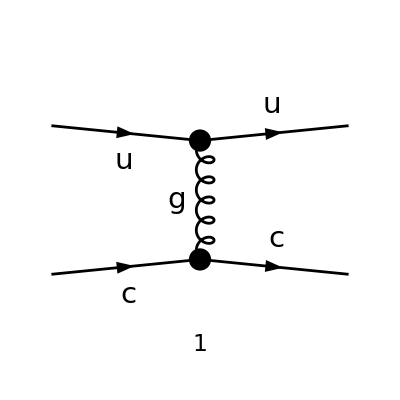

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{F[3,{1}],F[3,{2}]}->{F[3,{1}],F[3,{2}]},InsertionLevel->{Classes}, Model->"SMQCD",Restrictions->QCDOnly,ExcludeParticles->{F[1],V[2],V[3],V[1],S,SV,U[2],U[3],U[4],U[1]}];
Paint[diags,ColumnsXRows->{1,1},Numbering->Simple,SheetHeader->None,ImageSize->{256,256}];
```

```mathematica
amp0=FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True]//SUNSimplify[#,Explicit->True]&
```

-(g_s^2 T_Col3Col1^Glu5 T_Col4Col2^Glu5 (φ(OverBar[k_2],m_c)).(γ̄)^Lor2.(φ(OverBar[p2],m_c)) (φ(OverBar[k_1],m_u)).(γ̄)^Lor2.(φ(OverBar[p1],m_u)))/(OverBar[k_2]-OverBar[p2])^2

```mathematica
(*Below is a very stupid hack to extract the left- and right-handed components*)
```

```mathematica
ampLL=amp0//ReplaceAll[#,{Spinor[Momentum[k1],SMP["m_u"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k1],SMP["m_u"],1].(DiracGamma[LorentzIndex[Lor2]]-DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&//ReplaceAll[#,{Spinor[Momentum[k2],SMP["m_c"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k2],SMP["m_c"],1].(DiracGamma[LorentzIndex[Lor2]]-DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&;
```

```mathematica
ampLR=amp0//ReplaceAll[#,{Spinor[Momentum[k1],SMP["m_u"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k1],SMP["m_u"],1].(DiracGamma[LorentzIndex[Lor2]]-DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&//ReplaceAll[#,{Spinor[Momentum[k2],SMP["m_c"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k2],SMP["m_c"],1].(DiracGamma[LorentzIndex[Lor2]]+DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&;
```

```mathematica
ampRL=amp0//ReplaceAll[#,{Spinor[Momentum[k1],SMP["m_u"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k1],SMP["m_u"],1].(DiracGamma[LorentzIndex[Lor2]]+DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&//ReplaceAll[#,{Spinor[Momentum[k2],SMP["m_c"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k2],SMP["m_c"],1].(DiracGamma[LorentzIndex[Lor2]]-DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&;
```

```mathematica
ampRR=amp0//ReplaceAll[#,{Spinor[Momentum[k1],SMP["m_u"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k1],SMP["m_u"],1].(DiracGamma[LorentzIndex[Lor2]]+DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&//ReplaceAll[#,{Spinor[Momentum[k2],SMP["m_c"],1].DiracGamma[LorentzIndex[Lor2]]->1/2Spinor[Momentum[k2],SMP["m_c"],1].(DiracGamma[LorentzIndex[Lor2]]+DiracGamma[LorentzIndex[Lor2]].DiracGamma[5])}]&;
```

```mathematica
ampTot=v1 ampLL+v2 ampLR+v3 ampRL+v4 ampRR;
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,SMP["m_e"],SMP["m_mu"],SMP["m_e"],SMP["m_mu"]];
```

```mathematica
ampSquared[0]=Simplify[DiracSimplify[(FermionSpinSum[#1]&)[FeynAmpDenominatorExplicit[ampTot*ComplexConjugate[ ampTot]]]]]//SUNSimplify[#,Explicit->True]&
```

1/t^2 2 C_A C_F g_s^4 (2 m_c^2 (-2 m_e^2 (v1 v2+v3 v4)+4 m_u^2 (v1 v4+v2 v3)+t (v1 v2+v3 v4))-2 m_e^2 (-(m_μ^2 (v1^2+v2^2+v3^2+v4^2))+s (v1^2+v4^2)+u (v2^2+v3^2))+m_e^4 (v1^2+v2^2+v3^2+v4^2)-2 s v1^2 m_μ^2-2 s v4^2 m_μ^2+2 t v1 v3 m_u^2+2 t v2 v4 m_u^2-4 v1 v3 m_μ^2 m_u^2-2 u v2^2 m_μ^2-4 v2 v4 m_μ^2 m_u^2-2 u v3^2 m_μ^2+v1^2 m_μ^4+v2^2 m_μ^4+v3^2 m_μ^4+v4^2 m_μ^4+s^2 v1^2+s^2 v4^2+u^2 v2^2+u^2 v3^2)

```mathematica
Simplify[ampSquared[0]/.{SMP["m_e"]->0,SMP["m_c"]->0,SMP["m_u"]->0,SMP["m_mu"]->0}]//Simplify
```

(2 C_A C_F g_s^4 (s^2 (v1^2+v4^2)+u^2 (v2^2+v3^2)))/t^2